# CS298 - Differential Equations

## Kyle Perra - 7/16/2015

```mathematica
Clear[p,t,solution1]
```

```mathematica
solution1 = DSolve[{p'[t] == 0.1p[t],p[0]==100},p[t],t]
```

{{p[t]→100. ⅇ^(0.1 t)}}

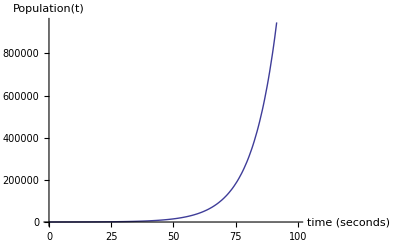

```mathematica
Plot[p[t]/.solution1,{t,0,100},AxesLabel->{"time (seconds)","Population(t)"},PlotRange->{{0,100},Automatic}]
```

## Bacteria Exercise

```mathematica
Clear[p,t,solution1]
solution1 = DSolve[{p'[t]==0.03p[t],p[0]==57},p[t],t]
```

{{p[t]→57. ⅇ^(0.03 t)}}

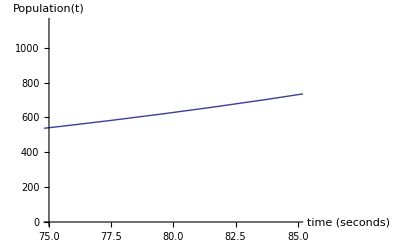

```mathematica
Plot[p[t]/.solution1,{t,0,100},AxesLabel->{"time (seconds)","Population(t)"},PlotRange->{{75,85},Automatic}]
```

Solution = ~625 (at time 80)

```mathematica
Manipulate[Module[{selectedChoice=Which[
substance=="radon-222",330350,
substance=="uranium-235",22200000000000000,
substance=="radium-226",50000000000]},Plot[amount E^(-1/selectedChoice*n),{n,.1,selectedChoice t},AxesOrigin->{0,0},ImageSize->{500,300},AxesLabel->{"time (seconds)","N(t)"},PlotLabel->Row[{"Half-Life = ",selectedChoice," seconds"}],PlotRange->{Automatic,Automatic},Filling->Bottom]],{{t,2,"time t"},1,8,1,Appearance->"Labeled"},{{amount,500,"StartingAmount"},100,1000,1,Appearance->"Labeled"},{substance,{"radium-226","radon-222","uranium-235"}}]
```